```mathematica
αx[θ_]:= Cos[θ]
αy[θ_]:= 1-Cos[θ]-Sin[θ]
αz[θ_]:= -Sin[θ]
βx[θ_]:= 2*Sin[θ]^2
βy[θ_]:=2*Sin[θ]^2*Tan[θ]
βz[θ_]:= 0
γx[θ_]:= Cos[θ]
γy[θ_]:= Cos[θ]^2
γz[θ_]:= Sin[θ]
```

```mathematica
vα[θ_]:= √(D[αx[θ],θ]^2+D[αy[θ],θ]^2+D[αz[θ],θ]^2)
vβ[θ_]:= √(D[βx[θ],θ]^2+D[βy[θ],θ]^2+D[βz[θ],θ]^2)
vγ[θ_]:= √(D[γx[θ],θ]^2+D[γy[θ],θ]^2+D[γz[θ],θ]^2)
```

```mathematica
vα[θ]
```

√(Cos[θ]^2+Sin[θ]^2+(-Cos[θ]+Sin[θ])^2)

```mathematica
vβ[θ]
```

√(16 Cos[θ]^2 Sin[θ]^2+(4 Sin[θ]^2+2 Tan[θ]^2)^2)

```mathematica
vγ[θ]
```

√(Cos[θ]^2+Sin[θ]^2+4 Cos[θ]^2 Sin[θ]^2)

```mathematica
vα[θ_]:=√(Cos[θ]^2+Sin[θ]^2+(-Cos[θ]+Sin[θ])^2)
vβ[θ_]:=√(16 Cos[θ]^2 Sin[θ]^2+(4 Sin[θ]^2+2 Tan[θ]^2)^2)
vγ[θ_]:=√(Cos[θ]^2+Sin[θ]^2+4 Cos[θ]^2 Sin[θ]^2)
```

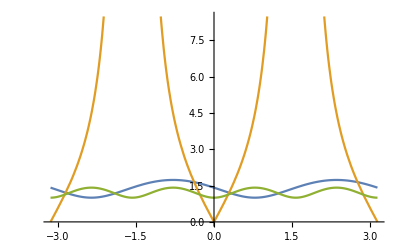

```mathematica
Plot[{vα[θ],vβ[θ],vγ[θ]},{θ,-π,π}, PlotRange->Automatic]
```

```mathematica
ParametricPlot3D[{{αx[θ],αy[θ],αz[θ]},{βx[θ],βy[θ],βz[θ]},{γx[θ],γy[θ],γz[θ]}},{θ,-2 π,2 π},AxesLabel->{x,y,z},PlotLabel->"Trajectories", PlotLegends-> {"α(θ)", "β(θ)", "γ(θ)"}]
```

-Graphics3D-

```mathematica
Export["1c.jpeg", ParametricPlot3D[{{αx[θ],αy[θ],αz[θ]},{βx[θ],βy[θ],βz[θ]},{γx[θ],γy[θ],γz[θ]}},{θ,-2 π,2 π},AxesLabel->{x,y,z},PlotLabel->"Trajectories", PlotLegends-> {"α(θ)", "β(θ)", "γ(θ)"}]]
```

1c.jpeg